Set the parameters of the system:

```mathematica
omega=2Pi
omega0 = 1.5 omega
beta=omega0/4
gamma = 1.073
```

2 π

9.42478

2.35619

1.073

Solve the actual differential equation:

```mathematica
s = NDSolve[
{

Phi''[t]+2beta Phi'[t]+omega0^2 Sin[Phi[t]]== gamma omega0^2 Cos[omega t],

Phi[0]==Pi/2,Phi'[0]==0},Phi,{t,0,50}]
```

{{Phi→InterpolatingFunction[{{0., 50.}}, <>]}}

Show the first few periods of the driving force:

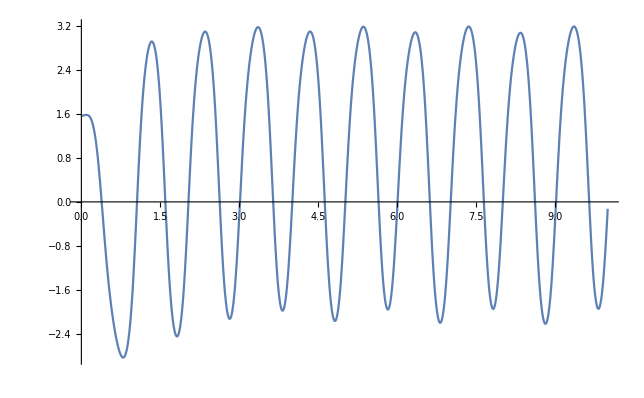

```mathematica
Plot[Evaluate[Phi[t]/.s],{t,0,10}, PlotRange -> All]
```

Show periods 30 to 40 of the driving force:

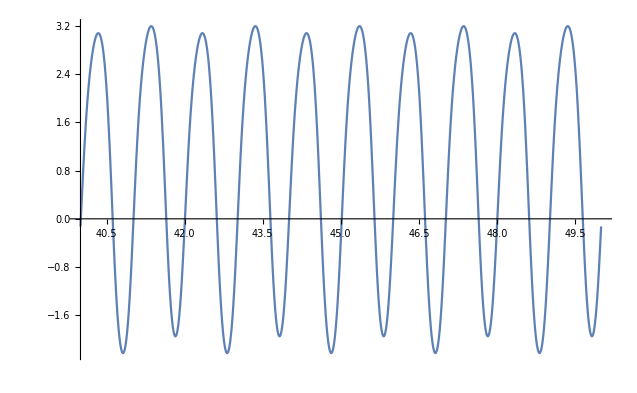

```mathematica
Plot[Evaluate[Phi[t]/.s],{t,40,50}, PlotRange -> All]
```

Get the values at integer multiples of the driving period:

```mathematica
Phi[{30,31,32,33,34,35,36,37,38,39,40}] /. s
```

{{-0.125809,-0.360619,-0.125809,-0.360618,-0.125809,-0.360618,-0.125809,-0.360619,-0.125809,-0.360619,-0.125809}}